```mathematica
data=Import["D:\\6 семестр\\Методы вычислений\\LR_2\\LR_2\\LR_2\\OUTPUT\\data.txt","Data"];
```

```mathematica
dataEx=Import["D:\\6 семестр\\Численные методы решения задач математической физики\\LR_2_new-master\\LR_2\\OUTPUT\\example3Ex.txt","Data"];
```

```mathematica
dataIm=Import["D:\\6 семестр\\Численные методы решения задач математической физики\\LR_2_new-master\\LR_2\\OUTPUT\\example3Im.txt","Data"];
```

```mathematica
dataMix=Import["D:\\6 семестр\\Численные методы решения задач математической физики\\LR_2_new-master\\LR_2\\OUTPUT\\example3Mix.txt","Data"];
```

```mathematica
data=data/Max[data];
```

```mathematica
BarLeg=BarLegend["TemperatureMap",Table[x,{x,0,1,0.001}]];
Manipulate[ArrayPlot[{data[[tau]]},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->False,PlotLegends->Placed[BarLeg,Below],PlotLabel->Style[τ==tau 0.01]],{tau,1,Length[data],5}]
```

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

```mathematica
gif=Table[ArrayPlot[{data[[tau]]},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->False,PlotLegends->Placed[BarLeg,Below],PlotLabel->Style[τ==tau 0.01]],{tau,1,Length[data],1}];
```

```mathematica
Export["D:\\6 семестр\\Методы вычислений\\LR_2\\tempgif1.gif",gif]
```

D:\6 семестр\Методы вычислений\LR_2\tempgif1.gif

```mathematica
Пример 3
```

```mathematica
sigma=2;
cappa=0.5;
cc=5;
u[x_,t_]:=If[x>=cc t,0,(sigma (cc /cappa) (cc t-x))^(1/sigma)]
```

```mathematica
xcomp=Table[x,{x,0,9.8,0.2}];
```

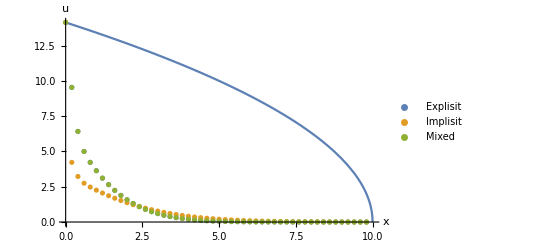

```mathematica
Show[Plot[(sigma cc/cappa (cc tt-xx))^(1/sigma),{xx,0,10},AxesLabel->{"x","u"}],ListPlot[{Transpose[{xcomp,dataEx[[-1]]}],Transpose[{xcomp,dataIm[[-1]]}],Transpose[{xcomp,dataMix[[-1]]}]},PlotRange->All,PlotLegends->{Explisit,Implisit,Mixed}]]
```

```mathematica
tt=1000 0.0002;
uu=Table[(sigma (cc /cappa) (cc tt-xx))^(1/sigma),{xx,0,10,0.2}];
```

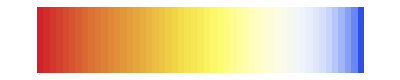

```mathematica
uu=uu/Max[uu];
ArrayPlot[{uu},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->False,PlotLegends->Placed[BarLeg,Below]]
```

```mathematica
Пример 0
```

```mathematica
u[x_,t_,lambda_]:=Sin[π x] Exp[- lambda t];
```

```mathematica
Manipulate[Plot[u[xx,tt,1],{xx,0,10},PlotRange->{{0,10},{-1,1}}],{tt,0,10}]
```

```mathematica
Manipulate[Plot[{u[xx,tt,0.5],u[xx,tt,1],u[xx,tt,2]},{xx,0,1},PlotRange->{{0,1},{-1,1}},PlotLegends->Automatic,AxesLabel->Automatic],{tt,0,10}]
```

```mathematica
data0Ex=Import["D:\\6 семестр\\Методы вычислений\\LR_2_new-master\\LR_2\\OUTPUT\\example0Ex.txt","Data"];
```

```mathematica
Manipulate[ListLinePlot[data0Ex[[tt]],PlotRange->{{0,Length[data0Ex[[1]]]+1},{-1,1}},AxesLabel->{"x","u"},PlotLabel->tt*0.01],{tt,1,Length[data0Ex],1}]
```

```mathematica
data0Ex[[500]]
```

{0,0.00213741,0.0040656,0.00559582,0.00657828,0.00691682,0.00657828,0.00559582,0.0040656,0.00213741,0}

```mathematica
uu=Table[u[xx,5,1],{xx,0,1,0.1}]
```

{0.,0.00208214,0.00396047,0.00545111,0.00640817,0.00673795,0.00640817,0.00545111,0.00396047,0.00208214,8.25161×10^-19}

```mathematica
Norm[data0Ex[[500]]-uu]
```

0.000399959